{{0.01,0,0},{0,0.0025,0},{0,0,0.0025}}

{{0.00016}}

0

7.90569

-2.68204

4.90476

0

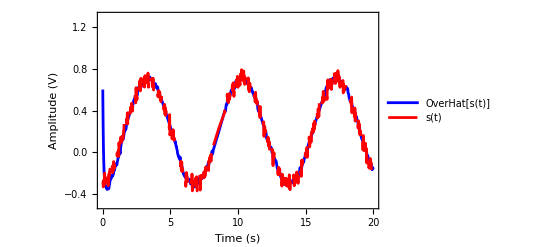

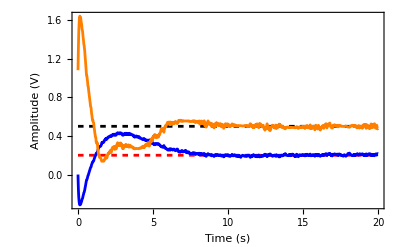

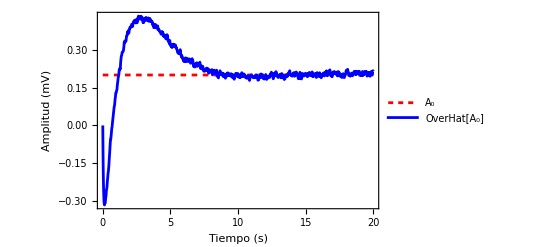

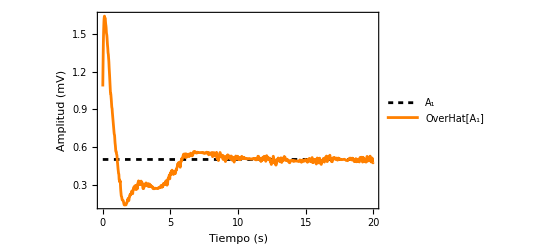

```mathematica
ClearAll["Global`*"]
A1=0.5;
θ1=30;


w=0.9;

(*tf=20;
dt=0.01;
puntos=Range[0,tf,dt];
valoresRuido=RandomVariate[NormalDistribution[0,0.05],Length[puntos]];
v2=Interpolation[Transpose[{puntos,valoresRuido}],InterpolationOrder->0] *)

n=1;
DesvEdo1=0.1;
DesvEdo2=0.05;
(*Qw=DesvEdo1^2 IdentityMatrix[2n];*)
Qw={{DesvEdo1^2,0,0},{0,DesvEdo2^2,0},{0,0,DesvEdo2^2}}
DesvObs=0.04;
Rv={0.1{DesvObs^2}}
aaa=00
dt=0.02;
sigma3=10;
tf=20;

(*DesvObs=0.2Am;*)
sigma3=DesvObs;
v2=Interpolation@Table[{t,RandomReal@NormalDistribution[0,sigma3]},{t,0,tf,dt}];



st=0.2+A1 Sin[w t+θ1] +v2[t];
k1=2; k2=3; 

A={{0,0,0},{0,0,w},{0,-w,0}};
B={{0},{0},{0}};
CC={{1,k1,k2}};

P=RiccatiSolve[{Transpose[A],Transpose[CC]},{Qw,Rv}];
L=P.Transpose[CC].Inverse[Rv];
l1=L[[1,1]]
l2=L[[2,1]]
l3=L[[3,1]]
a=00

y=x0[t]+k1 x1[t]+k2 x2[t];

Obs={
{x0'[t]==l1(st-y),x0[0]==0}, 
{x1'[t]==w x2[t] +l2(st-y),x1[0]==0.3}, 
{x2'[t]==-w x1[t]+l3(st-y),x2[0]==0}};

Ae1=Sqrt[(k1^2+k2^2)(x1[t]^2+x2[t]^2)];


Edo={x0[t],x1[t],x2[t]};
tf=20;
ss=NDSolve[{Obs},Edo,{t,0,tf},MaxSteps->∞];
Plot[Evaluate[{y,st}/.ss],{t,0,tf},PlotRange->{{0,tf},{-0.5,1.3}},PlotLegends->{Placed[{Style[OverHat["s(t)"]],"s(t)"},{Right,Top}]},PlotStyle->{Blue,{Red,Dashing[{0.07}]}},LabelStyle->{FontSize->14,Black},Frame->True,FrameLabel->{"Time (s)","Amplitude (V)"},FrameStyle->Black]

Show[
Plot[Evaluate[{0.2,x0[t]}/. ss],{t,0,tf},PlotRange->All,PlotLegends->{Placed[{"A_0",Style[OverHat["A_0"]]},{Right,Top}]},
PlotStyle->{{Red,Dashing[{0.01}]}, Blue},LabelStyle->{FontSize->14,Black},
Frame->True,FrameLabel->{"Time (s)","Amplitude (V)"},FrameStyle->Black],

Plot[Evaluate[{A1,Ae1}/. ss],{t,0,tf},PlotRange->All,PlotLegends->{Placed[{"A_1",Style[OverHat["A_1"]]},{Right,Top}]},PlotStyle->{{Black,Dashing[{0.01}]},Orange},LabelStyle->{FontSize->14,Black},Frame->True,FrameLabel->{"Tiempo (s)","Amplitud (mV)"},FrameStyle->Black]  
]



Show[
Plot[Evaluate[{0.2,x0[t]}/. ss],{t,0,tf},PlotRange->All,PlotLegends->{Placed[{"A_0",Style[OverHat["A_0"]]},{Right,Top}]},
PlotStyle->{{Red,Dashing[{0.01}]}, Blue},LabelStyle->{FontSize->14,Black},Frame->True,FrameLabel->{"Tiempo (s)","Amplitud (mV)"},FrameStyle->Black]
]

Show[
Plot[Evaluate[{A1,Ae1}/. ss],{t,0,tf},PlotRange->All,PlotLegends->{Placed[{"A_1",Style[OverHat["A_1"]]},{Right,Top}]},PlotStyle->{{Black,Dashing[{0.01}]},Orange},LabelStyle->{FontSize->14,Black},Frame->True,FrameLabel->{"Tiempo (s)","Amplitud (mV)"},FrameStyle->Black]  ]
```

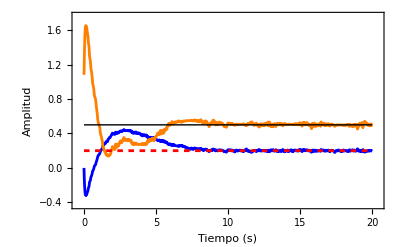

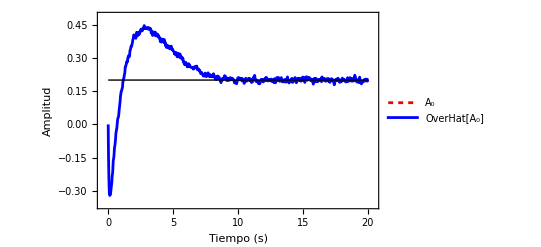

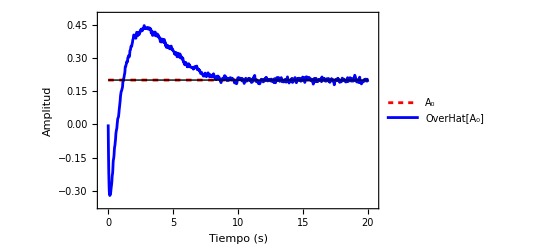

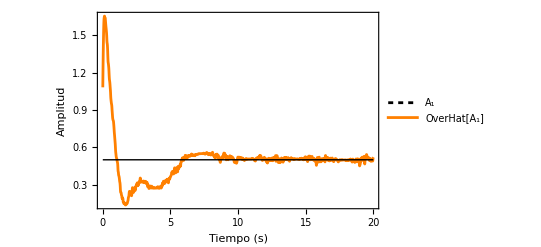

-Graphics-